```mathematica
GroundProjection[N_,Xmax_]:=Module[{A1,A2,H1,H2,v1,v2},
A1= Table[RandomReal[],{i,N},{j,N}];
H1 = I/4*(A1-Transpose[A1]);
A2= Table[RandomReal[Xmax],{i,N},{j,N}];
H2 = I/4*(A2-Transpose[A2]);
v1 =Eigensystem[H1][[2]][[1]];
v2= Eigensystem[H2][[2]][[1]];
Dot[Conjugate[v1],v2]/Sqrt[Dot[Conjugate[v1],v1]]/Sqrt[Dot[Conjugate[v2],v2]]
]
```

```mathematica
GroundProjectionDist[NM_,I_,Xmax_]:= Module[{dataList,para},
dataList = {};
For[i=0,i<I,i++,AppendTo[dataList,Abs[GroundProjection[2*NM,Xmax]]]];
Histogram[dataList,Automatic,"Probability"]
]
```

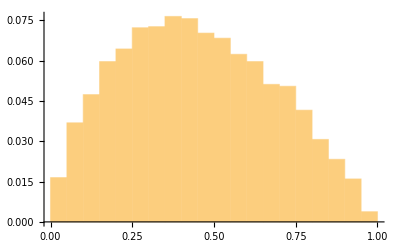
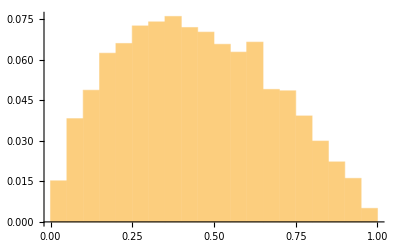
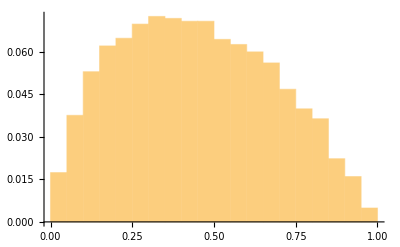
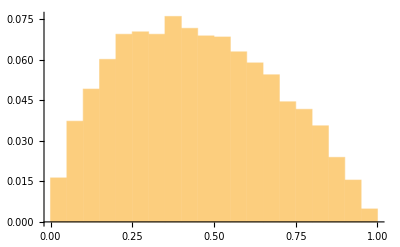
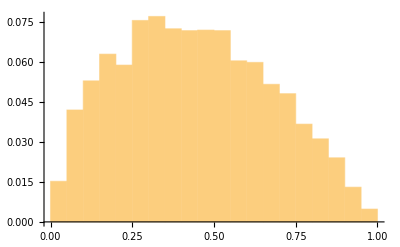

```mathematica
Table[GroundProjectionDist[2,10000,i],{i,1,5}]
```

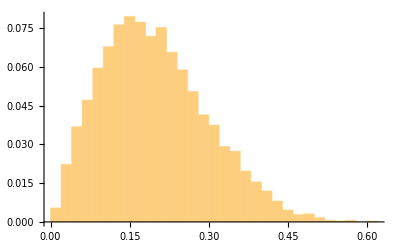
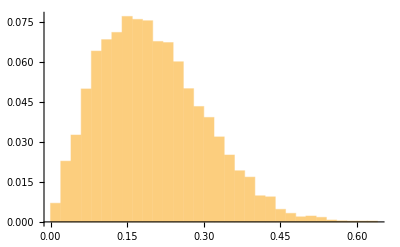
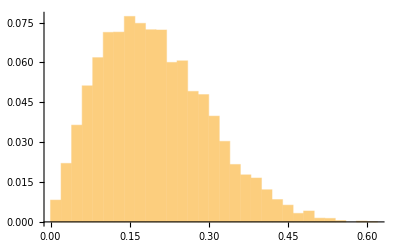
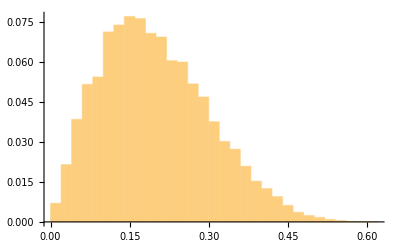
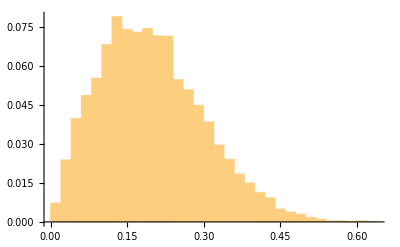

```mathematica
Table[GroundProjectionDist[10,10000,i],{i,1,5}]
```

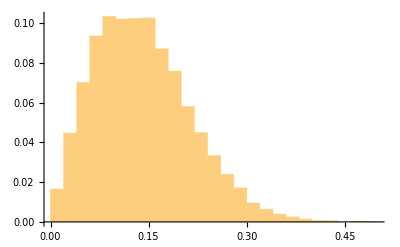
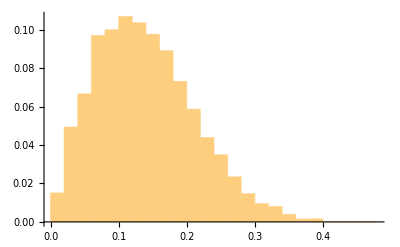
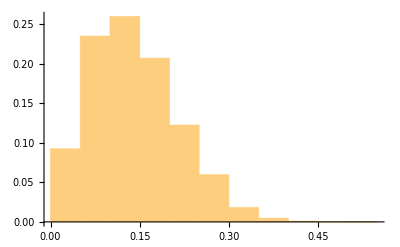
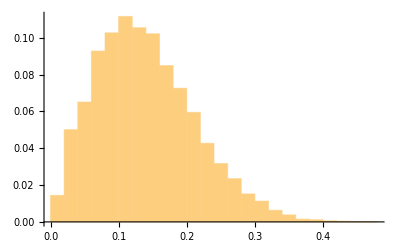
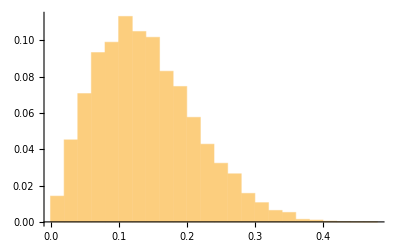

```mathematica
Table[GroundProjectionDist[20,10000,i],{i,1,5}]
```